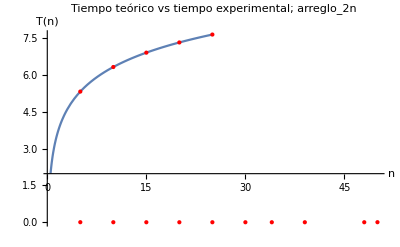

```mathematica
T[n_,a_]:=a Log2[n]+3;
f=Plot[T[n,0.0001],{n,0,25}];
puntos={{5,T[5,1]},{10,T[10,1]},{15,T[15,1]},{20, T[20,1]},{25, T[25,1]}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Red},AxesLabel->{"Eje X","Eje Y"},PlotRange->All];
Show[funcionFactorial,graficaPuntos,graficaPuntosNano, PlotRange->All,PlotLabel->"Tiempo teórico vs tiempo experimental; arreglo_2n", 
AxesLabel->{"n","T(n)"}]
```

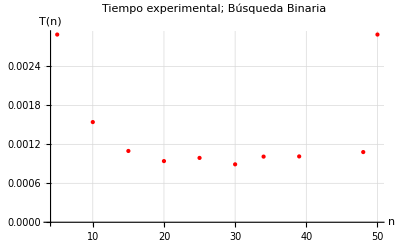

```mathematica
puntosNano={{5, 0.002891},{10,0.001543 },{15,0.001098},{20,0.000942 },{25,0.000991 },{30, 0.000892},{34,0.001011 },{39,0.001014 },{48, 0.001081},{50,0.002891 }};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Red},AxesLabel->{"n","T(n)"},PlotRange->All, PlotLabel->"Tiempo experimental; Búsqueda Binaria", GridLines->Automatic]
```

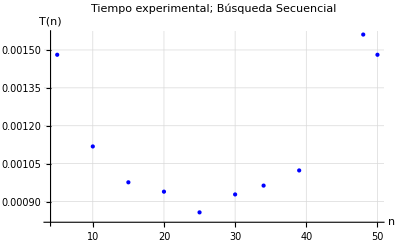

```mathematica
puntosNano={{5,0.001481},{10,0.001118 },{15,0.000976},{20,0.000939 },{25, 0.000857},{30,0.000928 },{34,0.000963 },{39,0.001023 },{48,0.001561 },{50,0.001481 }};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Blue},AxesLabel->{"n","T(n)"},
PlotRange->All, PlotLabel->"Tiempo experimental; Búsqueda Secuencial", GridLines->Automatic]
```